```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<TheDiractionary`
dict = RandomSample[Import["CSW21.txt", "List"]];
wordsByLength = GroupBy[dict, StringLength];
```

## Version 1: 7 Letter Scrabble-gorithm

### Run Algorithm

```mathematica
RunVersion1Scrabblegorithm[1]
```

Attempt 1

Bingos Found: {WONNERS}

Tiles Left: 93 AAAAAAAAABBCCDDDDEEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNOOOOOOOPPQRRRRRSSSTTTTTTUUUUVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS}

Tiles Left: 86 AAAAAAABCCDDDDEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNOOOOOOOPPQRRRRSSTTTTTTUUUVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS}

Tiles Left: 79 AAAAAABCDDDDEEEEEEEEEEFFGGGHHIIIIIIIIJKLLLLMMNNNNOOOOOOOPPQRRRTTTTTTUUVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS,CLADDED}

Tiles Left: 72 AAAAABDEEEEEEEEEFFGGGHHIIIIIIIIJKLLLMMNNNNOOOOOOOPPQRRRTTTTTTUUVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS,CLADDED,REBEGAN}

Tiles Left: 65 AAAADEEEEEEEFFGGHHIIIIIIIIJKLLLMMNNNOOOOOOOPPQRRTTTTTTUUVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS,CLADDED,REBEGAN,RUPTURE}

Tiles Left: 58 AAAADEEEEEEFFGGHHIIIIIIIIJKLLLMMNNNOOOOOOOPQTTTTTVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS,CLADDED,REBEGAN,RUPTURE,INTAGLI}

Tiles Left: 51 AAADEEEEEEFFGHHIIIIIIJKLLMMNNOOOOOOOPQTTTTVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS,CLADDED,REBEGAN,RUPTURE,INTAGLI,EDITING}

Tiles Left: 44 AAAEEEEEFFHHIIIIJKLLMMNOOOOOOOPQTTTVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS,CLADDED,REBEGAN,RUPTURE,INTAGLI,EDITING,MINIATE}

Tiles Left: 37 AAEEEEFFHHIIJKLLMOOOOOOOPQTTVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS,CLADDED,REBEGAN,RUPTURE,INTAGLI,EDITING,MINIATE,TOOLKIT}

Tiles Left: 30 AAEEEEFFHHIJLMOOOOOPQVVWXYYZ??

Bingos Found: {WONNERS,BAUERAS,CUIRASS,CLADDED,REBEGAN,RUPTURE,INTAGLI,EDITING,MINIATE,TOOLKIT,PLAYOFF}

Tiles Left: 23 AEEEEHHIJMOOOOQVVWXYZ??

No Valid Words

```mathematica
dataV1=CloudGet["V.1-WordMaster"];
```

```mathematica
Dataset[dataV1]
```

### Visualize

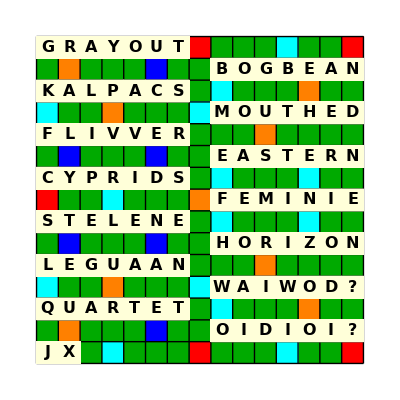

```mathematica
VisualizeVersion1[#]&/@RandomSample[dataV1,1]
```

## Version 2: 8 Letter Scrabble-gorithm

### Run Algorithm

```mathematica
RunVersion2Scrabblegorithm[1]
```

Bingos: {CUVETTE}

Tiles Left: 93 AAAAAAAAABBCDDDDEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTTTUUUVWWXYYZ??

Tiles Used: 7 CEETTUV

VITICETA played through: V

Bingos: {CUVETTE,VITICETA}

Tiles Left: 86 AAAAAAAABBDDDDEEEEEEEEEFFGGGHHIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTUUUVWWXYYZ??

Tiles Used: 14 ACCEEEIITTTTUV

DEATHIER played through: A

Bingos: {CUVETTE,VITICETA,DEATHIER}

Tiles Left: 79 AAAAAAAABBDDDEEEEEEEFFGGGHIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRSSSSTUUUVWWXYYZ??

Tiles Used: 21 ACCDEEEEEHIIIRTTTTTUV

ZYGAENID played through: I

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID}

Tiles Left: 72 AAAAAAABBDDEEEEEEFFGGHIIIIIIJKLLLLMMNNNNNOOOOOOOOPPQRRRRRSSSSTUUUVWWXY??

Tiles Used: 28 AACCDDEEEEEEGHIIINRTTTTTUVYZ

SISTRUMS played through: U

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS}

Tiles Left: 65 AAAAAAABBDDEEEEEEFFGGHIIIIIJKLLLLMNNNNNOOOOOOOOPPQRRRRSUUUVWWXY??

Tiles Used: 35 AACCDDEEEEEEGHIIIIMNRRSSSTTTTTTUVYZ

JEHADISM played through: D

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM}

Tiles Left: 58 AAAAAABBDDEEEEEFFGGIIIIKLLLLNNNNNOOOOOOOOPPQRRRRUUUVWWXY??

Tiles Used: 42 AAACCDDEEEEEEEGHHIIIIIJMMNRRSSSSTTTTTTUVYZ

GARGANEY played through: Y

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM,GARGANEY}

Tiles Left: 51 AAAABBDDEEEEFFIIIIKLLLLNNNNOOOOOOOOPPQRRRUUUVWWXY??

Tiles Used: 49 AAAAACCDDEEEEEEEEGGGHHIIIIIJMMNNRRRSSSSTTTTTTUVYZ

FALLOWED played through: E

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM,GARGANEY,FALLOWED}

Tiles Left: 44 AAABBDEEEEFIIIIKLLNNNNOOOOOOOPPQRRRUUUVWXY??

Tiles Used: 56 AAAAAACCDDDEEEEEEEEFGGGHHIIIIIJLLMMNNORRRSSSSTTTTTTUVWYZ

OPTIONAL played through: T

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM,GARGANEY,FALLOWED,OPTIONAL}

Tiles Left: 37 AABBDEEEEFIIIKLNNNOOOOOPQRRRUUUVWXY??

Tiles Used: 63 AAAAAAACCDDDEEEEEEEEFGGGHHIIIIIIJLLLMMNNNOOOPRRRSSSSTTTTTTUVWYZ

ADORABLY played through: A

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM,GARGANEY,FALLOWED,OPTIONAL,ADORABLY}

Tiles Left: 30 ABEEEEFIIIKNNNOOOOPQRRUUUVWX??

Tiles Used: 70 AAAAAAAABCCDDDDEEEEEEEEFGGGHHIIIIIIJLLLLMMNNNOOOOPRRRRSSSSTTTTTTUVWYYZ

OVERWEAK played through: R

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM,GARGANEY,FALLOWED,OPTIONAL,ADORABLY,OVERWEAK}

Tiles Left: 23 BEEFIIINNNOOOPQRRUUUX??

Tiles Used: 77 AAAAAAAAABCCDDDDEEEEEEEEEEFGGGHHIIIIIIJKLLLLMMNNNOOOOOPRRRRSSSSTTTTTTUVVWWYYZ

OVERFINE played through: V

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM,GARGANEY,FALLOWED,OPTIONAL,ADORABLY,OVERWEAK,OVERFINE}

Tiles Left: 16 BIINNOOPQRUUUX??

Tiles Used: 84 AAAAAAAAABCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIJKLLLLMMNNNNOOOOOOPRRRRRSSSSTTTTTTUVVWWYYZ

OPSONIUM played through: M with a blank S

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM,GARGANEY,FALLOWED,OPTIONAL,ADORABLY,OVERWEAK,OVERFINE,OPSONIUM}

Tiles Left: 9 BINQRUUX?

Tiles Used: 91 AAAAAAAAABCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIJKLLLLMMNNNNNOOOOOOOOPPRRRRRSSSSTTTTTTUUVVWWYYZ?

RUBICUND played through: C with a blank D

Bingos: {CUVETTE,VITICETA,DEATHIER,ZYGAENID,SISTRUMS,JEHADISM,GARGANEY,FALLOWED,OPTIONAL,ADORABLY,OVERWEAK,OVERFINE,OPSONIUM,RUBICUND}

Tiles Left: 2 QX

Tiles Used: 98 AAAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPRRRRRRSSSSTTTTTTUUUUVVWWYYZ??

Success!

```mathematica
dataV2=CloudGet["V.2-WordMaster"];
```

```mathematica
Dataset[RandomSample[CloudGet["V.2-WordMaster"],5]]
```

```mathematica
Dataset[dataV2]
```

### Visualize

```mathematica
data=RandomChoice[dataV2]
```

<|Bingos→{TINCHEL,TONETTES,EKISTICS,ANIMATES,WEENIEST,DEVELOPE,HALLOWER,PRANDIAL,OVERNAME,GUARDDOG,BOOBYISH,JANIZARY,FURFUROL,QUADDING},Overlaps→{T,E,I,S,E,H,L,A,D,S,N,R,D},Blanks→{L,N},Tiles Remaining→{I,X}|>

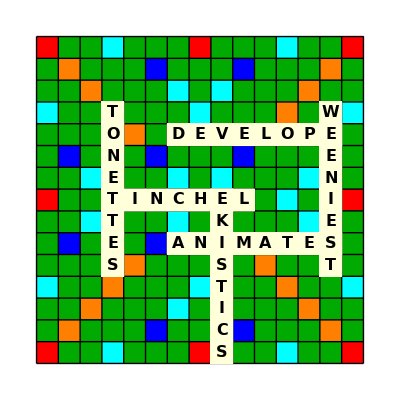

```mathematica
VisualizeVersion2[game_]:=Module[{epilog,board=CreateInitialScrabbleBoard[],bingos=game["Bingos"]},(*Place Bingos on board.*)
epilog=UpdateScrabbleBoard[bingos[[1]],{"H",4},"Right",{}];
epilog=UpdateScrabbleBoard[bingos[[2]],{"D",4},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[3]],{"H",9},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[4]],{"J",7},"Right",epilog];
epilog=UpdateScrabbleBoard[bingos[[5]],{"D",14},"Down",epilog];
epilog=UpdateScrabbleBoard[bingos[[6]],{"E",7},"Right",epilog];
Show[board,ImageSize->400,Epilog->epilog]
]

VisualizeVersion2[data]
```

## Version 3: Actual Scrabble Game

```mathematica
(* Initialize. *)
board=CreateInitialScrabbleBoard[]; (* Create Graphic of Empty Scrabble Board. *)
assoc=<||>;
starters=RandomSample[wordsByLength[7],50];
(* Turn 1. *)
i=1;
While[Length[assoc]==0,
remainingCounts=tiles[[All,"Quantity"]]; (* Whole tile bag remaining. *)
usedCounts=AssociationThread[Keys[tiles],Table[0,27]]; (* Initially zero tiles have been used. *)
Module[{next=False},
pos={"H",2};(*RandomChoice[Table[{"H",col},{col,2,8,1}]];*) (* Random position in row H. User could choose? *)
word=starters[[i]];
If[UpdateRemainingTileCount[remainingCounts,word,0]===tiles[[All,"Quantity"]], (* Starting 7-letter word must not require blanks. *)
Print[word, ": Choose another Starter"];
next=True
];

Module[{boardTurn1},
   boardTurn1=
    Row[
{
DynamicModule[
{currentBoard=board,localEpilogState},
localEpilogState=UpdateScrabbleBoard[word,pos, "Right",{}];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->localEpilogState],
	Button[
		"Select",
		AppendTo[assoc,1-><|"Bingo"->word,"Position"->pos,"Direction"->"Right"|>];
		remainingCounts = remainingCounts=UpdateRemainingTileCount[remainingCounts,word,0];
		usedCounts=UpdateUsedTileCount[usedCounts,word];
		epilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
		NotebookDelete[EvaluationCell[]];
		]
	}]
	],
Button["Skip",next=True;NotebookDelete[EvaluationCell[]]]}
];
If[next==False,Print[boardTurn1]];
WaitUntil[next===True];
next=False;
   ];
];
i++;
If[i>Length[starters],Abort[]]
]

(* Turns 2-12. *)
i=1;
While[1<=Length[assoc]<12,
Module[{next=False},(* Initialize flag. *)
  word=wordsByLength[8][[i]]; 
  overlapTileOptions= Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]];
  If[overlapTileOptions==={},Print[word," Has No Overlaps!"]; next=True];

Map[ (* Check the remaining counts for each overlap option. *)
If[
UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],0]==remainingCounts,
overlapTileOptions=DeleteCases[overlapTileOptions,#] (* Keep only options that can be formed with the available tiles. *)
]&,overlapTileOptions
];
If[overlapTileOptions==={},next=True];
overlapVectors=FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
If[overlapVectors==={}, next=True];
possibleEpilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,overlapVectors];
  
  Module[{boardOptions},
   boardOptions=
    Row[
Join[
Table[
      DynamicModule[
{currentBoard=board,localEpilogState,dIdx=idx},
localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
	Button[
		"Select",
		AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
		remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],0];
		usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
		epilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
		Print["Bingos Checked: ",i];
		NotebookDelete[EvaluationCell[]]
		]
	}]
	],
{idx,Length[overlapVectors]}],
{If[overlapTileOptions=!={},Button["Skip",next=True;NotebookDelete[EvaluationCell[]]],Nothing]}
]
];
If[next==False,Print[boardOptions]];
WaitUntil[next===True];
next=False;
   ];
  ];
i++; 
If[i==10000,Print["25% Bingos Checked"]];
If[i==20000,Print["50% Bingos Checked"]];
If[i==30000,Print["75% Bingos Checked"]];
If[i>Length[wordsByLength[8]],Abort[]];
]

(* Turns 13 and 14. *)
i=1;
While[Length[assoc]<14,
Module[{next=False},(* Initialize flag. *)
  word=wordsByLength[8][[i]];
(* Compute overlap tile options *)
  overlapTileOptions=Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]; 
b=BlanksAllowed[assoc,usedCounts];
 If[overlapTileOptions==={},
    Print[word," Has No Overlaps!"];
    next=True
  ];
  blankAssoc={};
  (* Identify blanks and update blankAssoc. *)
  Map[
    Module[{newRemainingCounts,negativeKeys},
	newRemainingCounts=UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b];
	If[newRemainingCounts==remainingCounts,
        overlapTileOptions=DeleteCases[overlapTileOptions,#],
	negativeKeys=Flatten[Table[#,{-newRemainingCounts[#]}]&/@Select[Keys[newRemainingCounts],newRemainingCounts[#]<0&]];
        If[negativeKeys=!={},
         AppendTo[blankAssoc,<|"Overlap"->#,"Blank"->negativeKeys|>],
	AppendTo[blankAssoc,<|"Overlap"->#,"Blank"->Null|>]
        ]
      ]
    ]&,
    overlapTileOptions
  ];

If[overlapTileOptions==={},next=True];
overlapVectors=FindPossibleOverlapPositions[assoc,word,overlapTileOptions];
If[overlapVectors==={}, next=True,
Echo@word;
{overlapVectors,possibleEpilogs} =
Module[
{vectors,epilogs,
blankVectors,wordOptions,blankEpilogs},
vectors=Select[overlapVectors,IdentifyBlanks[#,blankAssoc]==Null&];
epilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],epilogState]&,vectors];

blankVectors=Select[overlapVectors,IdentifyBlanks[#,blankAssoc]=!=Null&];
blankVectors=Map[Append[#,IdentifyBlanks[#,blankAssoc]]&,blankVectors];
wordOptions=AssociationMap[FormatWordWithBlanks[word,IdentifyBlanks[#,blankAssoc]]&,blankVectors];
blankEpilogs=AssociationMap[UpdateScrabbleBoard[StringReplace[wordOptions[#],c_/;LowerCaseQ[c]:>"?"],#[[1]],#[[2]],epilogState]&,blankVectors];
{Join[vectors,blankVectors],Join[epilogs,blankEpilogs]}
];
];

  Module[{boardOptions},
   boardOptions=
    Row[
Join[
Table[
      DynamicModule[
{currentBoard=board,localEpilogState,dIdx=idx},
localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
	Button[
		"Select",
		i=1;
		AppendTo[assoc,Length[assoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
		If[Length[overlapVectors[[dIdx]]]==5,
		usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->Flatten[{overlapVectors[[dIdx]][[3]],overlapVectors[[dIdx]][[5]]}]]]];
		remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],Length[overlapVectors[[dIdx]][[5]]]];
		Map[remainingCounts[#]++&,overlapVectors[[dIdx]][[5]]];
		usedCounts["?"]=usedCounts["?"]+Length[overlapVectors[[dIdx]][[5]]],
		usedCounts=UpdateUsedTileCount[usedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
		remainingCounts = UpdateRemainingTileCount[remainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],0]
		];
		epilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,usedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,remainingCounts]]]];
		NotebookDelete[EvaluationCell[]]
		]
	}]
	],
{idx,Length[overlapVectors]}],
{If[overlapTileOptions=!={},Button["Skip",next=True;NotebookDelete[EvaluationCell[]]],Nothing]}
]
];
If[next==False,Print[boardOptions]];
WaitUntil[next===True];
next=False;
   ];
  ];
i++; 
If[i==10000,Print["25% Bingos Checked"]];
If[i==20000,Print["50% Bingos Checked"]];
If[i==30000,Print["75% Bingos Checked"]];
If[i>Length[wordsByLength[8]],Abort[]];
]
```

Tiles Used: 7 AEKMRRS

Tiles Left: 93 AAAAAAAABBCCDDDDEEEEEEEEEEEFFGGGHHIIIIIIIIIJLLLLMNNNNNNOOOOOOOOPPQRRRRSSSTTTTTTUUUUVVWWXYYZ??

Tiles Used: 14 AEGKLMNOOPRRRS

Tiles Left: 86 AAAAAAAABBCCDDDDEEEEEEEEEEEFFGGHHIIIIIIIIIJLLLMNNNNNOOOOOOPQRRRSSSTTTTTTUUUUVVWWXYYZ??

Bingos Checked: 12

Tiles Used: 21 ADEEEGGIKLMMNNOOPRRRS

Tiles Left: 79 AAAAAAAABBCCDDDEEEEEEEEEFFGHHIIIIIIIIJLLLNNNNOOOOOOPQRRRSSSTTTTTTUUUUVVWWXYYZ??

Bingos Checked: 17

Tiles Used: 28 ACDEEEEGGGIIKLMMNNNOOPRRRSUY

Tiles Left: 72 AAAAAAAABBCDDDEEEEEEEEFFHHIIIIIIIJLLLNNNOOOOOOPQRRRSSSTTTTTTUUUVVWWXYZ??

Bingos Checked: 20

Tiles Used: 35 AAACDEEEEGGGIIJKLLLMMNNNOOPQRRRSUUY

Tiles Left: 65 AAAAAABBCDDDEEEEEEEEFFHHIIIIIIILNNNOOOOOOPRRRSSSTTTTTTUUVVWWXYZ??

Bingos Checked: 22

Tiles Used: 42 AAACCDDEEEEGGGIIJKLLLMMNNNOOOOPQRRRSTUUUWY

Tiles Left: 58 AAAAAABBDDEEEEEEEEFFHHIIIIIIILNNNOOOOPRRRSSSTTTTTUVVWXYZ??

Bingos Checked: 31

Tiles Used: 49 AAACCDDEEEEEGGGIIIIJKLLLMMNNNNOOOOPQRRRSSTTUUUWYZ

Tiles Left: 51 AAAAAABBDDEEEEEEEFFHHIIIIILNNOOOOPRRRSSTTTTUVVWXY??

Bingos Checked: 49

Tiles Used: 56 AAACCDDDDEEEEEEGGGIIIIJKLLLMMNNNNOOOOPQRRRRRSSTTUUUUVWYZ

Tiles Left: 44 AAAAAABBEEEEEEFFHHIIIIILNNOOOOPRSSTTTTVWXY??

Bingos Checked: 136

Tiles Used: 63 AAACCDDDDEEEEEEGGGIIIIIJKLLLLMMNNNNOOOOOOPQRRRRRRSSTTUUUUVVWYYZ

Tiles Left: 37 AAAAAABBEEEEEEFFHHIIIINNOOPSSTTTTWX??

Bingos Checked: 231

Tiles Used: 70 AAAAAABCCDDDDEEEEEEGGGHHIIIIIIJKLLLLMMNNNNOOOOOOPQRRRRRRSSTTUUUUVVWYYZ

Tiles Left: 30 AAABEEEEEEFFIIINNOOPSSTTTTWX??

Bingos Checked: 360

Tiles Used: 77 AAAAAABCCDDDDEEEEEEEFGGGHHIIIIIIIIJKLLLLMMNNNNOOOOOOPQRRRRRRSSSTTTTUUUUVVWYYZ

Tiles Left: 23 AAABEEEEEFINNOOPSTTWX??

Bingos Checked: 1251

Tiles Used: 84 AAAAAABCCDDDDEEEEEEEEEEFGGGHHIIIIIIIIIJKLLLLMMNNNNNOOOOOOPQRRRRRRSSSTTTTTTUUUUVVWYYZ

Tiles Left: 16 AAABEEFNOOPSWX??

Bingos Checked: 1258

SEABANKS

SNOWCAPS

SWEETSOP

SAPHENAS

ZAPATEOS

SABAYONS

ZABAJONE

SNEAKBOX

TUBENOSE

TOWPLANE

TONEPADS

TEASPOON

Tiles Used: 91 AAAAAAABCCDDDDEEEEEEEEEEEFGGGHHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTTTTTUUUUVVWYYZ

Tiles Left: 9 AABEFWX??

25% Bingos Checked

SWEATBOX

Tiles Used: 98 AAAAAAAABBCCDDDDEEEEEEEEEEEEFGGGHHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTTTTTUUUUVVWWXYYZ??

Tiles Left: 2 AF

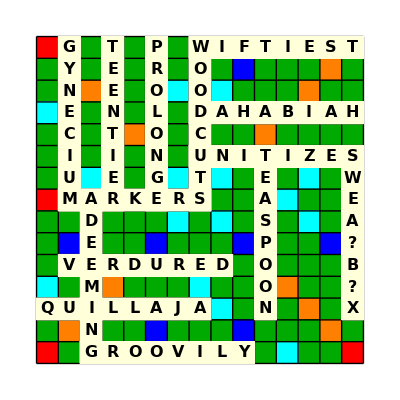

```mathematica
Show[board,Epilog->epilogState]
Dataset[assoc]
```

## TO DO:

1. Package up repetitive functionality.

## Debug: Styling of 2 of the same Blanks on Turn 14

#### Initialize

```mathematica
board=CreateInitialScrabbleBoard[];
debugAssoc=<|1-><|"Bingo"->"GLAZERS","Position"->{"H",2},"Direction"->"Right"|>,2-><|"Bingo"->"GONGLIKE","Position"->{"A",6},"Direction"->"Down","Overlap"->"E"|>,3-><|"Bingo"->"LIQUABLE","Position"->{"H",3},"Direction"->"Down","Overlap"->"L"|>,4-><|"Bingo"->"MAUNDING","Position"->{"A",2},"Direction"->"Down","Overlap"->"G"|>,5-><|"Bingo"->"BANDANNA","Position"->{"A",4},"Direction"->"Down","Overlap"->"A"|>,6-><|"Bingo"->"FOODWAYS","Position"->{"A",8},"Direction"->"Down","Overlap"->"S"|>,7-><|"Bingo"->"ZAPATEOS","Position"->{"H",5},"Direction"->"Down","Overlap"->"Z"|>,8-><|"Bingo"->"REFECTED","Position"->{"H",7},"Direction"->"Down","Overlap"->"R"|>,9-><|"Bingo"->"APOMIXES","Position"->{"F",8},"Direction"->"Right","Overlap"->"A"|>,10-><|"Bingo"->"DIORITIC","Position"->{"D",8},"Direction"->"Right","Overlap"->"D"|>,11-><|"Bingo"->"TOLARJEV","Position"->{"M",7},"Direction"->"Right","Overlap"->"T"|>,12-><|"Bingo"->"OUTTOWER","Position"->{"B",8},"Direction"->"Right","Overlap"->"O"|>,13-><|"Bingo"->"DERIVERS","Position"->{"O",7},"Direction"->"Right","Overlap"->"D"|>|>;
debugUsedCounts=<|"A"->9,"B"->2,"C"->2,"D"->4,"E"->11,"F"->2,"G"->3,"H"->0,"I"->8,"J"->1,"K"->1,"L"->4,"M"->2,"N"->6,"O"->8,"P"->2,"Q"->1,"R"->6,"S"->4,"T"->5,"U"->3,"V"->2,"W"->2,"X"->1,"Y"->1,"Z"->1,"?"->0|>;
debugRemainingCounts=<|"A"->0,"B"->0,"C"->0,"D"->0,"E"->1,"F"->0,"G"->0,"H"->2,"I"->1,"J"->0,"K"->0,"L"->0,"M"->0,"N"->0,"O"->0,"P"->0,"Q"->0,"R"->0,"S"->0,"T"->1,"U"->1,"V"->0,"W"->0,"X"->0,"Y"->1,"Z"->0,"?"->2|>;
debugEpilogState=;
Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,debugUsedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,debugUsedCounts]]]];
Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,debugRemainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,debugRemainingCounts]]]];
```

Tiles Used: 91 AAAAAAAAABBCCDDDDEEEEEEEEEEEFFGGGIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTTTTUUUVVWWXYZ

Tiles Left: 9 EHHITUY??

#### Test

```mathematica
i=1;
While[Length[debugAssoc]<14,
Module[{next=False},(* Initialize flag. *)
  word=wordsByLength[8][[i]];
(* Compute overlap tile options *)
  overlapTileOptions=Intersection[Characters[word],Flatten[KeyValueMap[Table[#1,#2]&,debugUsedCounts]]]; 
b=BlanksAllowed[debugAssoc, debugUsedCounts];
 If[overlapTileOptions==={},
    Print[word," Has No Overlaps!"];
    next=True
  ];
  blankAssoc={};
  (* Identify blanks and update blankAssoc. *)
  Map[
    Module[{newRemainingCounts,negativeKeys},
	newRemainingCounts=UpdateRemainingTileCount[debugRemainingCounts,StringJoin[DeleteElements[Characters[word],1->{#}]],b];
      If[newRemainingCounts==debugRemainingCounts,
        overlapTileOptions=DeleteCases[overlapTileOptions,#],
        negativeKeys=Flatten[Table[#,{-newRemainingCounts[#]}]&/@Select[Keys[newRemainingCounts],newRemainingCounts[#]<0&]];
        If[negativeKeys=!={},
         AppendTo[blankAssoc,<|"Overlap"->#,"Blank"->negativeKeys|>],
	AppendTo[blankAssoc,<|"Overlap"->#,"Blank"->Null|>]
        ]
      ]
    ]&,
    overlapTileOptions
  ];

If[overlapTileOptions==={},next=True];
overlapVectors=FindPossibleOverlapPositions[debugAssoc,word,overlapTileOptions];
If[overlapVectors==={}, next=True,
Echo@word;
Echo@blankAssoc;
{overlapVectors,possibleEpilogs} =
Module[
{vectors,epilogs,
blankVectors,wordOptions,blankEpilogs},
vectors=Select[overlapVectors,IdentifyBlanks[#,blankAssoc]==Null&];
epilogs=AssociationMap[UpdateScrabbleBoard[word,#[[1]],#[[2]],debugEpilogState]&,vectors];

blankVectors=Select[overlapVectors,IdentifyBlanks[#,blankAssoc]=!=Null&];
blankVectors=Echo@Map[Append[#,IdentifyBlanks[#,blankAssoc]]&,blankVectors];
wordOptions=AssociationMap[FormatWordWithBlanks[word,IdentifyBlanks[#,blankAssoc]]&,blankVectors];
blankEpilogs=AssociationMap[UpdateScrabbleBoard[StringReplace[wordOptions[#],c_/;LowerCaseQ[c]:>"?"],#[[1]],#[[2]],debugEpilogState]&,blankVectors];
{Join[vectors,blankVectors],Join[epilogs,blankEpilogs]}
];
];

  Module[{boardOptions},
   boardOptions=
    Row[
Join[
Table[
      DynamicModule[
{currentBoard=board,localEpilogState,dIdx=idx},
localEpilogState=possibleEpilogs[overlapVectors[[idx]]];
Column[{
	Show[currentBoard,ImageSize->300,Epilog->Dynamic[localEpilogState]],
	Button[
		"Select",
		i=1;
		AppendTo[debugAssoc,Length[debugAssoc]+1-><|"Bingo"->word,"Position"->overlapVectors[[dIdx]][[1]],"Direction"->overlapVectors[[dIdx]][[2]],"Overlap"->overlapVectors[[dIdx]][[3]]|>];
		  If[Length[overlapVectors[[dIdx]]]==5,
		debugUsedCounts=UpdateUsedTileCount[debugUsedCounts,StringJoin[DeleteElements[Characters[word],1->Flatten[{overlapVectors[[dIdx]][[3]],overlapVectors[[dIdx]][[5]]}]]]];
		debugRemainingCounts = UpdateRemainingTileCount[debugRemainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],Length[overlapVectors[[dIdx]][[5]]]];
		Map[debugRemainingCounts[#]++&,overlapVectors[[dIdx]][[5]]];
		debugUsedCounts["?"]=debugUsedCounts["?"]+Length[overlapVectors[[dIdx]][[5]]],
		debugUsedCounts=UpdateUsedTileCount[debugUsedCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]]];
		debugRemainingCounts = UpdateRemainingTileCount[debugRemainingCounts,StringJoin[DeleteElements[Characters[word],1->{overlapVectors[[dIdx]][[3]]}]],0]
		];
		debugEpilogState=localEpilogState;
		next=True;(* Flag is set to True when selected *)
		Print["Tiles Used: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,debugUsedCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,debugUsedCounts]]]];
		Print["Tiles Left: ",Length[Flatten[KeyValueMap[Table[#1,#2]&,debugRemainingCounts]]]," ",StringJoin[Flatten[KeyValueMap[Table[#1,#2]&,debugRemainingCounts]]]];
		NotebookDelete[EvaluationCell[]]
		]
	}]
	],
{idx,Length[overlapVectors]}],
{If[overlapTileOptions=!={},Button["Skip",next=True;NotebookDelete[EvaluationCell[]]],Nothing]}
]
];
If[next==False,Print[boardOptions]];
WaitUntil[next===True];
next=False;
   ];
  ];
i++; 
If[i==10000,Print["25% Bingos Checked"]];
If[i==20000,Print["50% Bingos Checked"]];
If[i==30000,Print["75% Bingos Checked"]];
If[i>Length[wordsByLength[8]],Abort[]];
]
```

EIGHTHLY

{<|Overlap→E,Blank→{G,L}|>,<|Overlap→G,Blank→{L}|>,<|Overlap→I,Blank→{G,L}|>,<|Overlap→L,Blank→{G}|>,<|Overlap→T,Blank→{G,L}|>,<|Overlap→Y,Blank→{G,L}|>}

{{{K,7},Right,E,REFECTED,{G,L}}}

EUTHYMIA

{<|Overlap→A,Blank→{M}|>,<|Overlap→E,Blank→{A,M}|>,<|Overlap→I,Blank→{A,M}|>,<|Overlap→M,Blank→{A}|>,<|Overlap→T,Blank→{A,M}|>,<|Overlap→U,Blank→{A,M}|>,<|Overlap→Y,Blank→{A,M}|>}

{{{K,7},Right,E,REFECTED,{A,M}}}

25% Bingos Checked

FRUITERY

{<|Overlap→F,Blank→{R,R}|>,<|Overlap→R,Blank→{F,R}|>}

{{{J,7},Right,F,REFECTED,{R,R}}}

EYESIGHT

{<|Overlap→E,Blank→{G,S}|>,<|Overlap→G,Blank→{E,S}|>,<|Overlap→S,Blank→{E,G}|>}

{{{K,7},Right,E,REFECTED,{G,S}}}

50% Bingos Checked

FUTILELY

{<|Overlap→F,Blank→{L,L}|>,<|Overlap→L,Blank→{F,L}|>}

{{{J,7},Right,F,REFECTED,{L,L}}}

ETHERIFY

{<|Overlap→E,Blank→{F,R}|>,<|Overlap→F,Blank→{E,R}|>,<|Overlap→R,Blank→{E,F}|>}

{{{K,7},Right,E,REFECTED,{F,R}}}

75% Bingos Checked

ETHERISH

{<|Overlap→E,Blank→{R,S}|>,<|Overlap→R,Blank→{E,S}|>,<|Overlap→S,Blank→{E,R}|>}

{{{K,7},Right,E,REFECTED,{R,S}}}

FUCHSITE

{<|Overlap→C,Blank→{F,S}|>,<|Overlap→F,Blank→{C,S}|>,<|Overlap→S,Blank→{C,F}|>}

{{{J,7},Right,F,REFECTED,{C,S}}}

EPIPHYTE

{<|Overlap→E,Blank→{P,P}|>,<|Overlap→P,Blank→{E,P}|>}

{{{K,7},Right,E,REFECTED,{P,P}}}

Tiles Used: 98 AAAAAAAAABBCCDDDDEEEEEEEEEEEEFFGGGHIIIIIIIIIJKLLLLMMNNNNNNOOOOOOOOPPQRRRRRRSSSSTTTTTTUUUVVWWXYYZ??

Tiles Left: 2 HU

## Visualize End Result

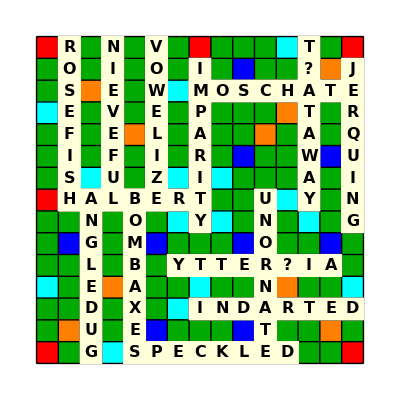

```mathematica
Dataset[assoc]
```

## Finding Words when Necessary

```mathematica
dict=RandomSample[Import["CSW21.txt","List"]];
wordsByLength=GroupBy[dict,StringLength];
```

```mathematica
Select[wordsByLength[8],First[Characters[#]]=="B"&]
```

{BURROWER,BILLFOLD,BIASINGS,BLURTING,BACKFLIP,BEATHING,BOLTHEAD,BOTRYTIS,BACKBEAT,BILLETEE,BECOWARD,BANTERER,BREVIERS,BRICKING,BUZZARDS,BARGELLO,BENTHOAL,BROODILY,BLOKEDOM,BONTEBOK,BIOWASTE,BEPITIES,BOUILLIS,BUSHBABY,BOTULINS,BACKSTAB,BARBOLAS,BIRLINNS,BOARDING,BELADIES,BULLYISM,BACHCHAS,BASSLINE,BERGMEHL,BORROWED,BEVELERS,BUSHVELD,BACKHOES,BIPARTED,BEHATTED,BISCUITY,BAROSAUR,BARRATER,BEMADDED,BREWAGES,BENEFITS,BANDSTER,BIOCYCLE,BAILOUTS,BASHMENT,BLENCHER,BOOKRACK,BEDRAILS,BROWSERS,BRASSILY,BEWILDER,BOATHOOK,BEDEGUAR,BRISKIER,BLASTOMA,BEDCHAIR,BOWLDERS,BABBLING,BRASIERS,BISEXUAL,BUOYAGES,BASEBALL,BEDABBLE,BROUGHTA,BUSTINGS,BIRDLIFE,BALMIEST,BACKLESS,BARMKINS,BEASTIES,BILGIEST,BLUEFISH,BENCHING,BRANNERS,BUNDLERS,BLANDISH,BLAGUERS,BLINTZES,BIENNIAL,BIOLYSIS,BELLWORT,BOARFISH,BIGHORNS,BERGAMAS,BLOTCHES,BEEFWOOD,BASALTIC,BRISURES,BARREING,BEANPOLE,BOBBYSOX,BLAWORTS,BLOWBACK,BOLTONIA,BEETLERS,BUMMLING,BLADIEST,BRIDOONS,BURNABLE,BOBECHES,BONEYARD,BACKBARS,BELONGER,BENETTED,BESMOKES,BLARNEYS,BIGAMIST,BROSIEST,BEAMIEST,BASIFIES,BORACHIO,BASEPATH,BLOWKART,BOEHMITE,BLUEGILL,BALLINGS,BLITHELY,BLEEDERS,BAGGIEST,BOOMBURB,BUTCHING,BIOPHORS,BULLHORN,BUFFALOS,BLONCKET,BITTINGS,BUBBLIER,BRUMBIES,BOTCHERS,BAYBERRY,BULLDOGS,BRODDLES,BELLCOTE,BULLDOZE,BLOWLAMP,BALDRICS,BOSHVARK,BLOKIEST,BOONDOCK,BEDRENCH,BARRETRY,BOORTREE,BOBWHITE,BOUDERIE,BERIMBAU,BEATLESS,BUMALOTI,BROWLESS,BEAUCOUP,BLOWZILY,BROASTED,BOHRIUMS,BLUNGING,BOWERIES,BARRATOR,BILOBATE,BLUEJACK,BOUCHEES,BLENDERS,BEMEANED,BIOPLASM,BLEARILY,BAKERIES,BRUSHOFF,BOLDENED,BOSOMING,BYSSUSES,BEARCATS,BABUCHES,BRONZING,BRONCHOS,BUGGERED,BILLHEAD,BLUSHING,BIRDFEED,BESOTTED,BOLLARDS,BLISTERY,BUSTLERS,BRITTLED,BAULKIER,BULLNECK,BARBICAN,BUCKINGS,BARRAGES,BRATTISH,BONAMIAS,BEGNAWED,BROCATEL,BLADDING,BULGINES,BUSTLINE,BIOLYSES,BREDRINS,BETTERED,BIRKIEST,BLUDGEON,BIRADIAL,BLUNKING,BRACIOLA,BASHLIKS,BLUNKERS,BLIGHTER,BROKENLY,BEZONIAN,BRAHMINS,BANDITTI,BANDANNA,BARRIEST,BRAMBLES,BROADEST,BORSTALS,BASSWOOD,BLAZONRY,BITCHING,BULLETIN,BUSHLOTS,BASIDIUM,BACKCHAT,BEMUDDLE,BAYFRONT,BREEZING,BRASSIES,BUNKMATE,BRELOQUE,BACKLOTS,BORSTALL,BESLIMES,BARRAGED,BUSYBODY,BACULUMS,BLEARING,BUCKEENS,BENEDICT,BARGEMEN,BACKWARD,BIOSCOPE,BIASEDLY,BEPRAISE,BEGALLED,BIRDSEED,BONTBOKS,BOWLINGS,BISCOTTI,BAUDEKIN,BACCHIAC,BATTERED,BARACANS,BRAAIING,BRUSHERS,BALLHAWK,BONEFISH,BALLGAME,BIRDLIKE,BAKEMEAT,BRODEKIN,BANNABLE,BEDRITES,BATAVIAS,BONKINGS,BACTERIC,BAKELITE,BRAIDING,BITSIEST,BARRETTE,BLACKING,BACKSLAP,BIWEEKLY,BLINDAGE,BOGGLING,BAYNODDY,BOMBORAS,BIGSTICK,BAALISMS,BAFFLERS,BANKSIDE,BEDPLATE,BREAKUPS,BRUNTING,BOGEYMEN,BROADAXE,BATTENER,BEMETING,BALLISTA,BLUEBIRD,BOLSHIES,BODINGLY,BRASTING,BLINDING,BOATFULS,BRUTINGS,BEEHIVES,BETACISM,BARELAND,BLUECAPS,BROWNEST,BARLEDUC,BLUETTES,BEDAZZLE,BLOKEISH,BLOGGING,BARBASCO,BENZOLES,BIDDABLY,BETRAYED,BADWARES,BEFINGER,BACKDOOR,BLATANCY,BACKVELD,BIGAMIES,BOGGARTS,BREINGES,BOSHBOKS,BARCODES,BUFFINGS,BOTFLIES,BUVETTES,BUTLERED,BLUSHETS,BUYABLES,BEMUFFLE,BEDAWINS,BEWORMED,BRASSARD,BENDIEST,BIGFOOTS,BEDSKIRT,BALLETED,BOLTLESS,BATWOMEN,BARWOODS,BIKEWAYS,BITCHIER,BREKKIES,BUTYRATE,BANOFFIS,BACKLIFT,BEPESTER,BEAUFFET,BRUCINES,BORSCHES,BESPREAD,BARKIEST,BOTHYMEN,BILANDER,BENTHONS,BORINGLY,BEDLAMER,BEGILDED,BOOKLICE,BOGGLERS,BEGORRAH,BLUESIER,BAULKERS,BOUVIERS,BARBWIRE,BURRATAS,BOATLIFT,BETREADS,BLANKEST,BRANKING,BOURKHAS,BRIERIER,BEDSONIA,BERSEEMS,BELLPULL,BEHEADED,BUCELLAS,BEDESMAN,BRISANCE,BERGENIA,BRIMFULL,BOYCOTTS,BUNODONT,BRUSHIER,BARCHANE,BLASTERS,BUSTARDS,BLOCKERS,BECLAMOR,BACKHAUL,BOROUGHS,BISNAGAS,BLOUSING,BIOPHORE,BLUEBACK,BEETROOT,BUCCINAS,BOSCAGES,BONDSMAN,BEERAGES,BALLONNE,BIRDCAGE,BISECTED,BEDIAPER,BUCKETED,BAVINING,BUCKTAIL,BULLFROG,BEARDING,BARBATED,BINARIES,BRYOZOAN,BANSELAS,BOURLAWS,BROCOLIS,BARRENLY,BAYSIDES,BIOASSAY,BUNGALOW,BOTANICS,BRUTISMS,BYPASSED,BYLANDER,BULIMIAC,BONUSING,BEDRAPED,BONDLESS,BROTHELS,BUSINESS,BOATBILL,BEWETTED,BLAFFING,BEATDOWN,BESMIRCH,BRONZIER,BOMBAXES,BEMURMUR,BUSSINGS,BELAYERS,BRANDADE,BIRDSEYE,BIOFILMS,BEAGLING,BAPTISMS,BANSHEES,BRITZKAS,BEFFANAS,BRAGGEST,BOINKING,BLOWDART,BLEAREST,BIMETHYL,BEERSIES,BEHOVING,BUCKSAWS,BRITZSKA,BEMUSING,BERDACHE,BARGOOSE,BIOPLAYS,BANDYMAN,BOBBLIER,BISTERED,BRAMBLED,BOREDOMS,BURSTONE,BUILDING,BECLOAKS,BUFFETER,BAITINGS,BESOGNIO,BETIMING,BAGPIPED,BEIGNETS,BEDMATES,BUSHELED,BANDEAUS,BEPELTED,BEHAVIOR,BRASHING,BOATNECK,BUHLWORK,BRANDING,BEDWARDS,BIRDSONG,BOMBYXES,BLOODILY,BRASEROS,BAGGAGES,BUCKRAKE,BEDUNCES,BABYDOLL,BREEZILY,BESTORMS,BOOTLAST,BACKHAND,BLESBUCK,BARDISMS,BANKSIAS,BARRACAN,BEDMAKER,BELLEEKS,BARRABLE,BRENNING,BURNSIDE,BATWOMAN,BLEEPERS,BIMBETTE,BUDGEROW,BLIZZARD,BOODLERS,BIOCIDAL,BLUEFINS,BREAKOUT,BULKHEAD,BOLDNESS,BOBBINET,BOATSMAN,BOVINELY,BLURBING,BERYLLIA,BALONEYS,BOSSDOMS,BOOTLACE,BURINIST,BORONIAS,BLATTERS,BEHAVERS,BOOBIRDS,BELABORS,BLUEBOOK,BEACHIER,BORDEAUX,BETHRALL,BEGUILER,BROWBONE,BUILDUPS,BLOODRED,BRASSART,BENDLETS,BLOODING,BEATINGS,BRATTIER,BRONCHUS,BLUSHERS,BAKLAVAS,BALDIEST,BEREAVES,BASTIDES,BALLBOYS,BYSTREET,BREENGES,BECRAWLS,BAILMENT,BATTLERS,BOBSTAYS,BULLIONS,BEFLEAED,BARONETS,BENDWAYS,BODYSUIT,BLETHERS,BELLYFUL,BACTERIN,BECURLED,BITINGLY,BRUCHIDS,BEDOUINS,BIGMOUTH,BERGYLTS,BUNCHING,BRULYIES,BARNLIKE,BULLWHIP,BURSTING,BAROMETZ,BIVALENT,BRASSISH,BOZZETTO,BOUNDERS,BIMORPHS,BRANDISH,BUSTIERS,BIRCHIRS,BLURRIER,BITTACLE,BECUDGEL,BEGUILES,BEMBIXES,BAGWORMS,BEADWORK,BASMATIS,BUPLEVER,BIDDINGS,BINAURAL,BRUNETTE,BIENNIUM,BETEEMED,BEDBOARD,BYCOKETS,BACILLUS,BEHOLDER,BALKINGS,BENZINES,BEHOOVES,BEARABLE,BOGYISMS,BESPEEDS,BEJABERS,BUFFABLE,BUSHMEAT,BONUSSED,BLITZING,BRUITING,BREGMATE,BACHATAS,BRACINGS,BOWERING,BABUDOMS,BRICKBAT,BIGEMINY,BLOSSOMS,BLUETITS,BATTIEST,BOOGYING,BELEAPED,BROGGING,BEARABLY,BOWWOWED,BONSELLA,BRINDLES,BEARDIES,BANISHES,BROCAGES,BERLEYED,BOTTINES,BEAVERED,BOOMKINS,BROMIDES,BEECHNUT,BAROSTAT,BOONGARY,BLISSING,BATHLESS,BORDELLO,BINATELY,BARONIES,BLUEBUCK,BOUNTIES,BRULZIES,BERGAMOT,BENZYLIC,BASELESS,BULLBARS,BLIMBING,BURNINGS,BEDFRAME,BEAGLERS,BEMIXING,BOGEYING,BANDARIS,BEELINED,BEROUGED,BERBERIN,BLASTULA,BAROCCOS,BRUNCHES,BLOWHARD,BLACKENS,BRAINIAC,BENDABLE,BALKIEST,BICUSPID,BURSTIER,BEKISSES,BLOOMING,BABBLIER,BEDSTAND,BLONDINE,BLACKEST,BOREALIS,BROWNERS,BAGELLED,BALAFONS,BLATTING,BARTSIAS,BLACKISH,BARCODED,BACKLAND,BIMBASHI,BRANCHED,BARGEMAN,BEMOUTHS,BALLYARD,BLOATERS,BLABBERS,BESTROWS,BEDROLLS,BOURTREE,BROMISED,BEMADAMS,BOTRYOID,BASELINE,BOERTJIE,BEADIEST,BROACHER,BATHMATS,BILLYBOY,BURBLERS,BUGSEEDS,BOOTIKIN,BDELLIUM,BALANCED,BASILISK,BROODERS,BILAYERS,BEERMATS,BOTHOLES,BRAKIEST,BULWARKS,BILLHOOK,BIRDCALL,BADLANDS,BANDYING,BLETTING,BOCACCIO,BULLSHOT,BRAIRDED,BEDDABLE,BLUBBERS,BOWHEADS,BAZAZZES,BOATSMEN,BLOCKIER,BRICKIER,BLACKGUM,BUTYROUS,BOYCHIKS,BARRENER,BOOMINGS,BEDSORES,BULBLETS,BAALEBOS,BUNCHILY,BIATCHES,BOSTHOON,BINNACLE,BELTLIKE,BUCKBEAN,BURLIEST,BICHROME,BEFOULED,BUTSUDAN,BIRACIAL,BEFLECKS,BEGUINES,BOLTLIKE,BOMBINGS,BEAUFETS,BUSKINGS,BICKERED,BALLADIN,BIOHERMS,BALDRICK,BARRINGS,BEMBEXES,BLACKBOY,BURGLING,BALLGOWN,BANKNOTE,BROMELIA,BIRIANIS,BOTANICA,BOLLOCKS,BONDABLE,BALLETIC,BUNDWALL,BONFIRES,BECHANCE,BIGNONIA,BALSAMIC,BIDARKAS,BILTONGS,BESTIALS,BETIDING,BATTUTAS,BANXRING,BANTLING,BEESTUNG,BRATCHET,BUFFERED,BEROBBED,BENDAYED,BLUENESS,BRISKEST,BLELLUMS,BUZZIEST,BIRDSHOT,BRABBLED,BOMBESIN,BICOLORS,BRUSKEST,BLUSTERS,BAWDIEST,BOARDMEN,BAASKAPS,BIBELOTS,BOOKWORK,BELCHERS,BLENCHES,BEDECKED,BLOODFIN,BENITIER,BURROWED,BEKISSED,BROMMERS,BESMILES,BURGOUTS,BEDSIDES,BOATPORT,BITTOCKS,BOLLWORM,BORRELIA,BURGHERS,BABASSUS,BIOTOXIN,BAGPIPES,BATTILLS,BECLOTHE,BANDITRY,BRANDERS,BACKWRAP,BEDRIVEL,BREINGED,BELIEVES,BUNTINGS,BEANBALL,BLANKIES,BERRIGAN,BEHIGHTS,BOOTLICK,BEDAZING,BOSQUETS,BLOODIES,BOMBARDS,BOASTFUL,BANKERLY,BABOUCHE,BRAINING,BLADDERY,BARTENDS,BANDLIKE,BIRETTAS,BEDASHED,BOOGEYED,BEREAVER,BALLGIRL,BEWRAYER,BAIDARKA,BEWHORED,BOASTERS,BALLSIER,BAGHOUSE,BACLOFEN,BUBBLING,BAUCHLES,BLOGGIER,BLATTANT,BLUEBILL,BOLTINGS,BEEFIEST,BIFORATE,BERCEUSE,BATHOSES,BLACKFIN,BOSCHBOK,BARGESTS,BURBLING,BONIBELL,BUDDLING,BARITONE,BAHOOKIE,BUSHFIRE,BOMBARDE,BACKINGS,BACKWORK,BANDINGS,BOGIEING,BIOCHIPS,BERGHAAN,BUSHPIGS,BERGERES,BITUMENS,BROWSIER,BROOKIES,BUCKAROO,BALISTAE,BARKLIKE,BESHREWS,BEVATRON,BROMELIN,BACKTALK,BULLNOSE,BOTTOMED,BEDSTEAD,BRANGLED,BRAZENRY,BOLSTERS,BLURTERS,BACULINE,BRIGHTLY,BRIARIER,BRITCHES,BATTELER,BAUDRICK,BEVELING,BLOUSONS,BEUNCLED,BRITTLER,BRIBABLE,BRANSLES,BEPOWDER,BRANCHER,BUZZINGS,BESMUTCH,BARGOONS,BARNEYED,BEAKIEST,BARRICOS,BAUBLING,BICEPSES,BEAKLESS,BREADIER,BANISHER,BRAILLES,BROIDERY,BREECHED,BENZOATE,BACILLAR,BLOATING,BOUGHTEN,BROGUISH,BACKROOM,BRAGGART,BLUEWING,BLEUATRE,BUGBANES,BLOKARTS,BEMAULED,BEMUZZLE,BEDUSTED,BOERBULL,BOMBSITE,BOLLOXES,BLOWIEST,BLUELINE,BEVVYING,BEERFEST,BLEATERS,BATTEAUX,BESLAVED,BITCHILY,BRISTLES,BUDDIEST,BARRANCO,BESIEGES,BREDRENS,BAVAROIS,BAGPIPER,BIFIDITY,BOYCHICK,BLUECOAT,BUTCHEST,BEDGOWNS,BLOGPOST,BUNCOING,BOYARISM,BRIGHTER,BODILESS,BRETTICE,BYLINING,BRADDING,BEWAILER,BLINDGUT,BEHEADER,BRAISING,BABYLIKE,BERETTAS,BUMBOATS,BEGIFTED,BRUXISMS,BOOKCASE,BOOKLIKE,BLIMPING,BUCARDOS,BUBBLIES,BANDAGER,BOYSIEST,BORTIEST,BALLPARK,BLOWTUBE,BEFOOLED,BLUESTEM,BRIGALOW,BELLOWER,BOOTLEGS,BELLBIRD,BALLADED,BREEDING,BELACING,BABIRUSA,BALLSING,BUSHGOAT,BEKNIGHT,BRIGHTEN,BOURDERS,BUNGLERS,BOWFRONT,BEHOVELY,BINDINGS,BESAINTS,BROMINES,BIOTRONS,BALLANTS,BIZNAGAS,BOOZINGS,BULKAGES,BLOTTERS,BORNITIC,BISCOTTO,BETTINGS,BAILABLE,BRAKEMEN,BRAWLING,BOLDFACE,BRATTLES,BANJAXES,BANISTER,BRASSETS,BOERBULS,BABELISH,BESHADOW,BANDELET,BREAKERS,BANDEAUX,BALADINS,BEDAGGLE,BARONIAL,BRAVADOS,BODYWASH,BONIFACE,BEMUDDED,BURSEEDS,BANDANAS,BABUSHKA,BETHANKS,BRECCIAS,BULLOCKS,BURKITES,BUBALINE,BONANZAS,BIOFUELS,BAZOUKIS,BIPLANES,BLINKARD,BOGEYISM,BREATHER,BRIGANDS,BULIMIAS,BORATING,BADGERED,BULLINGS,BLARTING,BRAVOING,BIRDFARM,BUSTIEST,BEJESUIT,BUGGIEST,BUZZCUTS,BARTISAN,BIRTHING,BEGUILED,BRAZENLY,BOILOFFS,BILIMBIS,BAREHEAD,BLUEJAYS,BEAUTEST,BOOHOOED,BENEDICK,BANJOIST,BESPEAKS,BATHROBE,BODHRANS,BREACHES,BASTIONS,BOMBLETS,BRAKEMAN,BEARINGS,BEFOAMED,BUGGANES,BEDAUBED,BASTILLE,BUMPKINS,BARRATRY,BELLINGS,BECKONED,BELCHING,BEAUTIFY,BHELPURI,BENISONS,BANDAGES,BENZIDIN,BARENESS,BEKNAVED,BLUFFEST,BENDINGS,BANDEIRA,BURGAGES,BALDHEAD,BUMBAZES,BESTROWN,BRAKEAGE,BALLONET,BLUGGIER,BAWCOCKS,BLAGGERS,BOUNDARY,BOXBERRY,BODYSIDE,BECARPET,BISERIAL,BARFLIES,BOOGYMAN,BURSTERS,BUTYRINS,BUNKERED,BATONING,BLOCKADE,BEASTILY,BEJEWELS,BECALMED,BOLTHOLE,BEEYARDS,BIFIDUMS,BANTERED,BIRYANIS,BURNOOSE,BICYCLER,BELLETER,BATOLOGY,BROADENS,BATTELED,BUFFOONS,BARBEQUE,BEZAZZES,BOTTLERS,BULKINGS,BORNEOLS,BUSUUTIS,BARROOMS,BRITTLES,BOSTANGI,BOUQUETS,BRIDLERS,BURDENER,BABBITRY,BAUXITIC,BARRACES,BEESTING,BANKSTER,BRONDEST,BEADSMEN,BETAKING,BOOKWORM,BROWBEAT,BEWARING,BILLOWED,BOGGARDS,BLOCKING,BEGROANS,BOUCLEES,BOGEYMAN,BROCADES,BUTTYMEN,BUSHELER,BOBBLING,BEAUXITE,BACKLASH,BACKFILL,BEDPOSTS,BROCARDS,BUNHEADS,BOISERIE,BUTYLENE,BROACHES,BABESIAS,BONHOMIE,BIBLISTS,BODGIEST,BOOTJACK,BIPRISMS,BOTRYOSE,BUMSTERS,BENTWOOD,BACKDOWN,BACKRUSH,BARBITAL,BAREGINE,BENISEED,BREVISES,BLEEPING,BLUDIEST,BAILBOND,BANALITY,BEATNIKS,BAREBONE,BEAMLESS,BRIDLING,BLOCKIES,BIOTITIC,BUNDLING,BLANDEST,BULLERED,BARKEEPS,BRINNIES,BACKREST,BOUSOUKI,BONDMAID,BOBWHEEL,BEDLAMPS,BLEWARTS,BLOWINGS,BELFRIES,BARCHANS,BLAUBOKS,BONNIEST,BIGUINES,BANNERET,BAGARRES,BEFUDDLE,BOOKLORE,BOODLING,BIOTYPIC,BACCHANT,BARBULES,BLAUDING,BUGABOOS,BACCARAS,BREACHED,BROWNOUT,BODYLINE,BULLDUST,BANGALOW,BETATTER,BUFFIEST,BRIGADED,BOOBOOKS,BITEABLE,BEREAVED,BABYFOOD,BUMPIEST,BIACETYL,BASHLESS,BAWDRIES,BUTCHERY,BURBLIER,BACKSPIN,BONSPIEL,BRABBLER,BLIMPISH,BELOVEDS,BRIDEMEN,BASTINGS,BUTYLATE,BENCHTOP,BEDTIMES,BROMATED,BUDGEROS,BESCREEN,BIRDBATH,BAULKILY,BIOBANKS,BANISHED,BARNACLE,BURGHULS,BLAGGING,BOBOTIES,BANDPASS,BAKESHOP,BLESSERS,BLOODIED,BREERING,BANNINGS,BIGARADE,BACKBOND,BLAMEFUL,BEBOPPER,BODIKINS,BOARDMAN,BRUNCHED,BROCADED,BIBULOUS,BATHCUBE,BISMARCK,BABELISM,BERRYING,BIRTHDAY,BEBLOODS,BARTERER,BARDSHIP,BURRAMYS,BAHADURS,BRISKING,BRACTEAL,BUZZSAWS,BARBARIC,BHANGRAS,BIHOURLY,BLOUBOKS,BAILSMEN,BOBOLINK,BLUEBEAT,BELABOUR,BURRFISH,BRACKENS,BEGLAMOR,BACKMOST,BOHEMIAN,BOHEMIAS,BESEEMED,BROWBAND,BOXBOARD,BEERNUTS,BOOKSIER,BOBFLOAT,BILBERRY,BRAGGING,BEBEERUS,BROIDERS,BLIGHTED,BRUISERS,BASSETED,BULWADDY,BONEMEAL,BOSSINGS,BITTIEST,BATTINGS,BARYONIC,BURGEONS,BUMFUCKS,BRAWNIER,BOBBITTS,BEARBINE,BORDURES,BOTULISM,BRACKISH,BUBBLERS,BANDSMAN,BESCOURS,BINDABLE,BOTANIZE,BASHTAGS,BUTTERED,BUSHLIKE,BOTHYMAN,BACTERIA,BOSKAGES,BREWSKIS,BIOPSIES,BERATING,BOUFFANT,BLINGEST,BOURSINS,BAUDRICS,BACKWASH,BUSHWALK,BURRITOS,BIANNUAL,BLOODIER,BACKSETS,BUCKEROO,BEDIMMED,BERNICLE,BANKROLL,BAINITES,BULLPENS,BEGGINGS,BURLETTA,BOUZOUKI,BOLLIXES,BLOOMERY,BITTERED,BATGIRLS,BITCOINS,BINOCLES,BROMISES,BLITHERS,BURLESKS,BRIMLESS,BATCHERS,BULLACES,BLOTLESS,BALDNESS,BURRIEST,BUZZWORD,BOULTERS,BEDHEADS,BLAZONED,BANGTAIL,BATHMISM,BASEBORN,BLENCHED,BLOWSIER,BEDTICKS,BIMENSAL,BANALIZE,BEVOMITS,BRAUNITE,BRABBLES,BROOCHED,BURKINIS,BAILSMAN,BICYCLED,BURGUNDY,BANALISE,BACKDATE,BEVELLER,BOOBHEAD,BLITZERS,BAUXITES,BATOONED,BLONDING,BALMLIKE,BRANCHIA,BRESAOLA,BONIATOS,BILEVELS,BOOFIEST,BAKEWARE,BALANCER,BLUCHERS,BANKRUPT,BACKWOOD,BEMOANER,BOWSHOTS,BOUNCING,BONASSUS,BUNDYING,BRIEFERS,BIOSOLID,BEMOANED,BARNWOOD,BLOSSOMY,BOURSIER,BLIPPING,BENJAMIN,BORACITE,BRUTALLY,BINARISM,BACULITE,BLINNING,BEEBREAD,BIVVYING,BUSHLESS,BEGAZING,BACKBURN,BUCOLICS,BEDOTTED,BERSERKS,BIRSLING,BRICOLES,BERGALLS,BOOTLESS,BIOMETRY,BUTANONE,BUCKLERS,BERIMING,BLASTOFF,BOASTING,BEARDIER,BEFLOWER,BABBLERS,BILLETED,BARRATED,BILLETER,BRUITERS,BAZOOKAS,BUSGIRLS,BAROGRAM,BORECOLE,BRASSAGE,BUCKLING,BEMADDEN,BACKSEYS,BRACKETS,BIRDINGS,BOBTAILS,BENCHERS,BALLADES,BEPLUMED,BAGASSES,BESHOUTS,BROMISMS,BONAMANI,BEDRIGHT,BUDGEREE,BOLSHIER,BASELOAD,BOOBYISM,BYWONERS,BEALINGS,BULLWEED,BEQUESTS,BACKBEND,BUCATINI,BERCEAUX,BIOGENIC,BOLTROPE,BEECHIER,BABICHES,BETEEMES,BISHOPED,BEDSOCKS,BOUDOIRS,BOBOLLED,BLISTERS,BURGONET,BITEWING,BLIMPERY,BUSLOADS,BESIGHED,BONNOCKS,BONELESS,BLUDGERS,BLOUSILY,BLANKETY,BESOOTHE,BESTREWN,BESMOKED,BRICKIES,BUGGINGS,BALLYHOO,BRASHIER,BONGOIST,BUILDERS,BRANNING,BROKAGES,BROCHURE,BISTABLE,BELOVING,BOOMTOWN,BEMOCKED,BINOMIAL,BROADISH,BLANDING,BOGWOODS,BESTOWAL,BRAWLERS,BISMUTHS,BIMANOUS,BOOMIEST,BOUNCERS,BLACKTOP,BLOOPIER,BALLCLAY,BRADOONS,BIOTOPES,BLANKING,BOOKFULS,BEARSKIN,BLEBBING,BEEFCAKE,BLOWOFFS,BOWYANGS,BEDUNCED,BENIGNER,BIJUGOUS,BLITTING,BESPORTS,BESIEGER,BRAZILIN,BIOPLAST,BROUGHAM,BACKHOED,BUZKASHI,BAWLINGS,BOYHOODS,BEMOILED,BLUEGOWN,BOGBEANS,BULGIEST,BLOTCHED,BULKIEST,BLINDEST,BRETHREN,BEPROSED,BOTTARGA,BRAILLED,BALUSTER,BRANDIES,BARGUEST,BOOKREST,BASALTES,BICYCLES,BATSWING,BONEYEST,BREAKOFF,BANNERED,BOOKINGS,BAULKING,BLOWZIER,BALLOCKS,BUKKAKES,BUZZKILL,BELTWAYS,BRISTLED,BUTTHEAD,BITSTOCK,BACKOUTS,BIELDING,BARKENED,BRIDGING,BEDCOVER,BALLIUMS,BRACHIAL,BRUNIZEM,BACKCOMB,BOOZIEST,BROLLIES,BALAYAGE,BUNTIEST,BUNDOOKS,BOFFOLAS,BLOGROLL,BEGIRDED,BLUEHEAD,BOREASES,BIDDABLE,BEATIEST,BEDEAFEN,BALLIEST,BADASSED,BLEACHES,BOGHOLES,BORKINGS,BANDEROL,BERYLINE,BEEHIVED,BLOGGERS,BARBETTE,BROOCHES,BEDUMBED,BILLABLE,BILABIAL,BUTANOLS,BALLASTS,BOWWOODS,BUYBACKS,BEDRAPES,BULLSHIT,BLASTING,BOOKLETS,BROILING,BURGRAVE,BLADINGS,BOUNCILY,BURRELLS,BACKFALL,BUDGETED,BECHARMS,BIFORMED,BUTTRESS,BASELARD,BREATHED,BLOUSIER,BASHLYKS,BLUNGERS,BLATHERS,BENOMYLS,BIBLICAL,BEDARKEN,BEEFALOS,BAYADERE,BRAZIERY,BOLLIXED,BISECTOR,BACKBITE,BACCATED,BINDWEED,BETHINKS,BANKCARD,BOURGEON,BRACTLET,BEACHING,BELLHOPS,BLINKERS,BESPOKEN,BOILABLE,BLOWJOBS,BENEFACT,BOTCHILY,BANLIEUE,BRINKMEN,BANSHIES,BANDURAS,BECURSED,BEACHBOY,BROWNIER,BOTCHING,BERAYING,BOXTHORN,BARBOTTE,BRINGING,BONINESS,BIOGRAPH,BACKWALL,BEDASHES,BLUNTEST,BOPPIEST,BRUSQUER,BORLOTTI,BOMBASTS,BEATABLE,BEADINGS,BILLYCAN,BOOTHOSE,BECROWDS,BRODDING,BIRDWING,BASEHEAD,BELAMOUR,BONAMANO,BARMPOTS,BERHYMED,BAUDRONS,BLACKFLY,BELEEING,BEHAPPEN,BLINGING,BORESOME,BOTCHIER,BIRCHING,BEDDINGS,BEFOULER,BEHEADAL,BUCKHORN,BORAZONS,BIZARROS,BOBSKATE,BLUNTISH,BRUHAHAS,BRANTAIL,BURNOUTS,BARRETOR,BESTRIDE,BOTONNEE,BOURREES,BESEEKES,BIRAMOUS,BRIONIES,BIOSCOPY,BAGNETTE,BEDUNGED,BUTMENTS,BISCUITS,BALLUTES,BATHINGS,BRYONIES,BENZENES,BREENGED,BLASTIES,BANDSAWS,BRAKINGS,BEDYEING,BLOWDOWN,BRANCHES,BIVALVES,BASTARDY,BERLINES,BASIFIER,BUILDOUT,BOUNDING,BROOKING,BOXHAULS,BROILERS,BULLSEYE,BOUTONNE,BECRIMED,BOTTLING,BRONCHIA,BANAUSIC,BUMELIAS,BROOKITE,BEWIGGED,BONEHEAD,BURDIZZO,BROCHING,BOTHRIUM,BANKABLE,BALDPATE,BROCHANS,BAFFLING,BEGGARLY,BOILINGS,BALLATED,BLURBIST,BOOFHEAD,BEGOTTEN,BLINGIER,BURRHELS,BIBATION,BORROWER,BACHELOR,BUCKSHOT,BARMAIDS,BONEBEDS,BEMINGLE,BUDDINGS,BECLOUDS,BUNGWALL,BUSYWORK,BAYWOODS,BESHAMES,BUSHINGS,BEVERAGE,BATCHING,BACKFATS,BEAKLIKE,BACKSTAY,BRAIDERS,BUCKAYRO,BLASTIER,BLOWPIPE,BLOOMIER,BEHOWLED,BESOULED,BEQUEATH,BETELNUT,BANGALAY,BIOFACTS,BOTANISE,BABBITTS,BACKFLOW,BARONNES,BRIOCHES,BESLAVES,BRANTLES,BHISTEES,BLUEBUSH,BESLIMED,BROMIZES,BENCHIER,BOOKLAND,BESMILED,BACCHIAN,BOUGHPOT,BLAMABLE,BUNRAKUS,BUDDYING,BLOOPERS,BOLIVARS,BEANBAGS,BEPEARLS,BAASKAAP,BUMMALOS,BRANNIER,BRINGERS,BARNIEST,BANQUETS,BREECHES,BELIQUOR,BOMBYCID,BAPTISIA,BOXPLOTS,BROCCOLI,BOUNTREE,BEARHUGS,BIRDDOGS,BACKSAWS,BROGUERY,BAPTISTS,BAUCHLED,BIOTROPH,BILLIARD,BALISTAS,BEDWARFS,BIMETALS,BASSETTS,BLOWOUTS,BAPTISED,BELAYING,BEDROCKS,BASILECT,BEHEMOTH,BRUSTING,BOOKENDS,BESPICED,BUSKINED,BUTTYMAN,BAPTISER,BRASSICA,BELLBOYS,BUBUKLES,BROOMIER,BRINDLED,BLENDING,BREVIARY,BAREBOAT,BRENTEST,BACKFIRE,BASENESS,BREEZIER,BEARWARD,BATELESS,BALEFIRE,BLABBING,BLOTTIER,BAGELING,BARWARES,BOOTABLE,BALMORAL,BEDBATHS,BIRTHDOM,BENIGHTS,BENUMBED,BOATABLE,BURNOUSE,BROTHIER,BUSTLING,BROMIDIC,BEGRIMED,BANDFISH,BEHOLDEN,BIGAMOUS,BATTUTOS,BIMESTER,BULLHEAD,BLEACHER,BAIRNISH,BARGAINS,BROMATES,BUMPERED,BOULDERS,BIKINIED,BOXINESS,BEFRINGE,BIRAMOSE,BLOBBIER,BROODIER,BIVINYLS,BARGHEST,BERAKING,BIRDLIME,BIONOMIC,BACKSTOP,BANTINGS,BETAINES,BESTREWS,BRAINISH,BUSHIEST,BAREHAND,BLUFFING,BLEAKISH,BESTRODE,BACKSIDE,BEHOTING,BONESETS,BERMUDAS,BAPTIZES,BINGOING,BEGINNER,BOOKIEST,BASSOONS,BLONDISH,BEPITIED,BIATHLON,BRUISING,BAGGINGS,BYRLAKIN,BORSCHTS,BICYCLIC,BACKSLID,BEGIRDLE,BAPTISES,BRONZERS,BELLOCKS,BLURRILY,BLUBBING,BRUSHING,BREACHER,BESHIVER,BELTINGS,BACKLOGS,BLAZERED,BLUSHFUL,BABELDOM,BEWINGED,BACRONYM,BONITOES,BETATRON,BEARLIKE,BESTEADS,BICAUDAL,BILLYOHS,BERINGED,BEGGARED,BESCRAWL,BREADBOX,BACALAOS,BLAZONER,BARYTONE,BALCONET,BANKBOOK,BEIGIEST,BISTOURY,BOREHOLE,BOILOVER,BRAHMANS,BEDUCKED,BEZZANTS,BESTOWER,BLUNTING,BOGGIEST,BREWISES,BOTARGOS,BIGAROON,BARBELLS,BOULTING,BONDINGS,BROWNISH,BLEACHED,BILLFISH,BULNBULN,BLOWBALL,BASSINET,BARATHEA,BERBERES,BEDEWING,BACKWIND,BEPROSES,BACLAVAS,BRETESSE,BEPIMPLE,BRINJALS,BINGLING,BOOKSHOP,BOTANIES,BEGULFED,BREWPUBS,BOSSISMS,BLUEWOOD,BIASNESS,BRISKETS,BENIGNLY,BANNEROL,BURGANET,BLOOSMED,BONUSSES,BIYEARLY,BALISAUR,BRIMMERS,BOURDONS,BIDARKEE,BATIKING,BATTALIA,BROKINGS,BUGBEARS,BIBIMBAP,BARISTAS,BANGSTER,BOGLANDS,BONELIKE,BEBOPPED,BRADAWLS,BRAILLER,BIOTITES,BLUESMEN,BRACONID,BADINAGE,BASEMENT,BERTHING,BUGHOUSE,BOLIVIAS,BLACKCAP,BADMOUTH,BEHAVING,BOMBABLE,BOWSPRIT,BROCKETS,BREEDERS,BAILLIES,BULLCOOK,BLANCHER,BOINGING,BEDIGHTS,BOATYARD,BOARDIES,BLOWHOLE,BETOILED,BRYOLOGY,BIBBINGS,BATTLEAX,BEANLIKE,BECRUSTS,BIGHTING,BRISLING,BECLOWNS,BIRIYANI,BROACHED,BIZAZZES,BORDERER,BRAWLIER,BERIBERI,BOWLLIKE,BLOTTING,BATHORSE,BAGUETTE,BRUCELLA,BLEAKEST,BEADLIKE,BREGMATA,BUTTLING,BUFFETED,BARRULET,BUCKRAMS,BUNGLING,BANDORES,BARTERED,BIFACIAL,BOURBONS,BESIEGED,BESEEMLY,BANDAGED,BERGFALL,BASILARY,BOUSIEST,BRAINIER,BIGENERS,BRINDISI,BESHINES,BLOBBING,BERASCAL,BEDSTRAW,BEDRESTS,BOTHERED,BOWKNOTS,BEDLINER,BALSAMED,BEWRAYED,BATTENED,BODEMENT,BRILLEST,BATISTES,BASCULES,BROWNING,BECRIMES,BAWDRICS,BOOGYMEN,BREAKING,BACKLIST,BUTYRYLS,BRUMMERS,BUSHWAHS,BIOMETER,BARBECUE,BESMOOTH,BOWHUNTS,BUTTOCKS,BEVELLED,BATHROOM,BRITSKAS,BEDROOMS,BAROQUES,BOLONEYS,BIFOCALS,BOUNTIED,BEAUFINS,BILINEAR,BACKBAND,BESTILLS,BREADTHS,BRANGLES,BECOMING,BETHUMBS,BLANKETS,BAUHINIA,BATEMENT,BANALEST,BALLPEEN,BALLCOCK,BATTLING,BACKWORD,BUOYANCY,BROUHAHA,BUTYRALS,BEFRIEND,BEMISTED,BIOMORPH,BITTERER,BALNEARY,BESUITED,BOONLESS,BEDQUILT,BUSYNESS,BRASILIN,BELTLESS,BELADIED,BRECCIAL,BLEATING,BULLYBOY,BURDENED,BETHUMPS,BESEEING,BRATPACK,BREVETED,BACCHIUS,BLUFFERS,BESPRENT,BOZZETTI,BUKSHEES,BRIGUING,BRAZENED,BLOWSILY,BRICKLES,BIVOUACS,BOOKLESS,BLOCKISH,BROWNIES,BASICITY,BUTTONED,BOOSTERS,BLESBOKS,BATHETIC,BEAUTIED,BOOBYISH,BRAZIERS,BARDLING,BRATTLED,BEFALLEN,BOUNCIER,BREASTED,BLASHING,BALADINE,BEMEDALS,BABYSITS,BUMMAREE,BIMANUAL,BARONESS,BUZZWIGS,BEETLING,BOWELLED,BRONZIFY,BRANDIED,BELIEVED,BILSTEDS,BRASHEST,BLOVIATE,BLISSFUL,BUNKOING,BASOPHIL,BACKBONE,BEGONIAS,BUNDISTS,BRINIEST,BABUISMS,BESTADDE,BURTHENS,BRIMMING,BRASSIER,BANDROLS,BONDAGER,BASEBAND,BABESIAE,BESTIARY,BETONIES,BETWEENS,BELLINIS,BESOUGHT,BETRAYAL,BASIFIED,BIOCLEAN,BALLOTED,BIRTHERS,BARBICEL,BLASTOID,BESTREAK,BAREFOOT,BIOETHIC,BOSKIEST,BELIEVER,BRAILING,BESNOWED,BEAUTIES,BISTROIC,BARRELED,BANGKOKS,BOURRIDE,BEFOGGED,BESCORCH,BOOKABLE,BESTOWED,BESHAMED,BACKLINE,BEERHALL,BELLCAST,BULLBATS,BRIMINGS,BLAMMING,BIDENTAL,BUMBAZED,BLURRING,BANDORAS,BITCHERY,BRIQUETS,BITESIZE,BIVALVED,BETOSSES,BACKYARD,BESPICES,BUDDLEIA,BALLOTEE,BEDAMNED,BANDYMEN,BLOWFISH,BLUSTERY,BITTOURS,BONNETED,BARBERRY,BHEESTIE,BIGHEADS,BIOLOGIC,BOMBLOAD,BLEBBIER,BEPUFFED,BENDWISE,BEFINNED,BLESSING,BISCACHA,BOXBALLS,BLOGRING,BASINFUL,BILLINGS,BIOVULAR,BABYHOOD,BRANCARD,BREATHES,BUISTING,BALLROOM,BITTERNS,BEADROLL,BURGLARY,BREVIATE,BISSONED,BRICHTER,BEGEMMED,BLOWGUNS,BOYISHLY,BANDITOS,BELLBIND,BARILLAS,BILLBUGS,BOXWOODS,BOLLOXED,BATTERER,BENEFICE,BATHTUBS,BARDIEST,BEPATTED,BIPAROUS,BELITTLE,BLINDERS,BATFOWLS,BONSPELL,BRIGADES,BESHROUD,BALLADIC,BLUENOSE,BUTANOIC,BUCKSHEE,BARYTONS,BEELINES,BRIEFING,BALANCES,BRISKISH,BASSISTS,BURSICON,BLANCOED,BRASSING,BONDAGES,BESTAINS,BAROUCHE,BURQUINI,BESORTED,BELLYING,BERTHAGE,BUNCOMBE,BINGEING,BOSSIEST,BEKNAVES,BILLBOOK,BULLSHAT,BARRACKS,BUZZBAIT,BUDWORMS,BELAMIES,BEMIRING,BOVINITY,BRODKINS,BUTCHERS,BUMFLUFF,BIOTECHS,BREWINGS,BANNOCKS,BIOTICAL,BOGARTED,BECURSES,BOATLOAD,BULLRUSH,BROOKLET,BATTEROS,BEHALVES,BRUSSELS,BURGLARS,BEWHORES,BACCARAT,BELFRIED,BIASSING,BRISTOLS,BARTIZAN,BARRANCA,BULLOCKY,BASSIEST,BETITLES,BOWINGLY,BULLIEST,BYLINERS,BAKEOFFS,BARMIEST,BOUTIQUE,BLUEGUMS,BRACHAHS,BOOGALOO,BARGEESE,BERBERIS,BEDERALS,BEACONED,BEDIZENS,BOUTADES,BOOKMARK,BETOSSED,BARKHANS,BUSHBUCK,BEGLOOMS,BERRETTA,BADGERLY,BICONVEX,BRAWNILY,BUMPINGS,BESOMING,BUNGHOLE,BESLAVER,BOATLIKE,BLUDGING,BAWDKINS,BULIMIES,BASOCHES,BLANQUET,BRACELET,BENZOYLS,BURWEEDS,BYPLACES,BALLYRAG,BUSHLAND,BEGRIMES,BLEEDING,BUNCHIER,BLUEWEED,BUDWOODS,BLACKTIP,BEGHARDS,BORNITES,BUMBLERS,BASCINET,BIBCOCKS,BONDSMEN,BEVERING,BALLOONS,BESETTER,BLANCHED,BROCKRAM,BLINKING,BAKLAWAS,BEGRUDGE,BUBINGAS,BEGUNKED,BECASSES,BAYADEER,BLUEBELL,BEWAILED,BESMEARS,BREWSTER,BIJUGATE,BRACHIUM,BIRRETTA,BRIDEMAN,BANOFFEE,BRONZITE,BACKFILE,BRACCATE,BETHESDA,BRISKENS,BRUCITES,BURETTES,BROCKAGE,BEJUMBLE,BANJAXED,BOOMLETS,BIENNALE,BOWELING,BACKSEAT,BADASSES,BAKSHISH,BLADDERS,BARSTOOL,BUXOMEST,BEPOMMEL,BIOBLAST,BETOKENS,BEDSHEET,BUNFIGHT,BHISHTIS,BUMMOCKS,BRACIOLE,BROKERED,BUDGETER,BEHOOVED,BUGWORTS,BHISTIES,BEPAINTS,BELDAMES,BEGINNES,BREAMING,BIFORKED,BACONERS,BELTLINE,BIZARRES,BLEARIER,BUNTLINE,BRANDISE,BEZIQUES,BROODING,BENADRYL,BULLRING,BEARWOOD,BUOYANCE,BIRROTCH,BARONAGE,BITURBOS,BIOTYPES,BOTTOMER,BESONIAN,BIRLINGS,BANDSMEN,BESTICKS,BRUILZIE,BUTTONER,BAPTIZER,BANKSMAN,BULGHURS,BRAHMANI,BOOKBAGS,BOBSLEDS,BIJWONER,BOTTEGAS,BULIMICS,BIOCIDES,BEZZLING,BULLPOUT,BLIPVERT,BRECHANS,BULLYING,BIOPSIED,BOOSTING,BODYWORK,BELATING,BOARDERS,BEEFLESS,BUNCHERS,BASTILES,BEINNESS,BALLOTER,BRAGGERS,BIOGASES,BUCKSKIN,BLOCKAGE,BOATTAIL,BLANCHES,BISTORTS,BASENJIS,BEARPAWS,BRANKIER,BARRIQUE,BELGARDS,BIZCACHA,BICKERER,BLUETICK,BASINETS,BASIDIAL,BLENNIES,BLOOPING,BROEKIES,BEDESMEN,BETRAYER,BACCALAS,BEDIMPLE,BELLOWED,BUCCALLY,BOWLFULS,BEFITTED,BAMBINOS,BAPTIZED,BLAMABLY,BOURDING,BLABBIER,BETHORNS,BAWNEENS,BAASSKAP,BANKSMEN,BRECHAMS,BOSOMIER,BINGINGS,BRIDALLY,BLONDEST,BRATTICE,BODYSURF,BOLIXING,BOUILLON,BARRIERS,BOLOGNAS,BRAINILY,BUMBLING,BAYONETS,BENTIEST,BEAMLIKE,BAREBACK,BETROTHS,BLUEINGS,BUSULFAN,BECAPPED,BIELDIER,BLUBBERY,BRODDLED,BETHWACK,BREADING,BABBELAS,BRACEROS,BLUIDIER,BREADNUT,BYPASSES,BRACHETS,BASHINGS,BESMUDGE,BESPOUTS,BROOMING,BECHALKS,BUSHIDOS,BETITLED,BLASHIER,BUSHTITS,BECALLED,BULRUSHY,BANTENGS,BRAVURAS,BARKLESS,BASANITE,BLUESMAN,BROTHERS,BEADSMAN,BASSNESS,BEASTING,BEREAVEN,BARNYARD,BALLADRY,BLAGUEUR,BIPHASIC,BREAKAGE,BOULDERY,BOBOWLER,BEAMLETS,BOXROOMS,BLUEBALL,BLOOMERS,BRAGGIER,BATELEUR,BIRSIEST,BACKPACK,BENAMING,BLITHEST,BILLIONS,BANDIEST,BRAEHEID,BULLGINE,BROMANCE,BASILICA,BARBERED,BRUNCHER,BITRATES,BREADBIN,BURLEYED,BOWLINES,BELLBUOY,BLACKOUT,BALKLINE,BASQUINE,BLACKLEG,BRAINPAN,BREASKIT,BONSELAS,BEESWING,BRAINBOX,BEATIFIC,BLUNDERS,BIGGINGS,BEDEVILS,BEPEPPER,BACKDROP,BANDMATE,BURSITIS,BICOLOUR,BARESARK,BENZOINS,BICORNES,BOTANIST,BAITFISH,BOODYING,BOTTOMRY,BECHAMEL,BRATLING,BONGRACE,BROWSING,BORDERED,BURDOCKS,BRIEFEST,BESPOUSE,BIOLYTIC,BRAIDEST,BABYMOON,BEAMINGS,BROMIZED,BACKACHE,BECKONER,BOTCHERY,BECLASPS,BEERIEST,BELONGED,BASTARDS,BUCKEYES,BRINKMAN,BEJEEZUS,BRUSHUPS,BABYCINO,BETTONGS,BAILIFFS,BACKFITS,BROADWAY,BULLYRAG,BERHYMES,BIPHENYL,BESWARMS,BLOOSMES,BASKETRY,BARBLESS,BANDOOKS,BEJADING,BACALHAU,BANKINGS,BLASTEMA,BIUNIQUE,BULLETED,BATTERIE,BLITTERS,BOATINGS,BREVETCY,BEGETTER,BELAUDED,BACKLOAD,BITTERLY,BACKCAST}

## Prove it is Solvable

```mathematica
blocks=Table[
  StringJoin[Table[" ",If[num==1,7,8]]],
  {num,1,14}
];
BingoIndex[pos_,num_,dir_,epilogState_] :=
Module[{ x=(pos[[2]]-1),y=15-(LetterNumber[pos[[1]]]-1)},
Append[epilogState,Text[Column[{Style[ToString[num],12,Bold],Style[ToString[dir],12,Bold]},Center,0],{x+0.5,y-0.5}]]
]
board=CreateInitialScrabbleBoard[];
```

```mathematica
epilog={};
epilog=UpdateScrabbleBoard[blocks[[1]], {"H",2}, "Right",epilog];
epilog=BingoIndex[{"H",2},1,"→",epilog];
turns[1]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[2]], {"A",3}, "Down",epilog];
epilog=BingoIndex[{"A",3},2,"↓",epilog];
turns[2]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[3]], {"A",5}, "Down",epilog];
epilog=BingoIndex[{"A",5},3,"↓",epilog];
turns[3]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[4]], {"A",8}, "Down",epilog];
epilog=BingoIndex[{"A",8},4,"↓",epilog];
turns[4]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[5]], {"A",7}, "Right",epilog];
epilog=BingoIndex[{"A",7},5,"→",epilog];
turns[5]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[6]], {"C",7}, "Right",epilog];
epilog=BingoIndex[{"C",7},6,"→",epilog];
turns[6]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[7]], {"E",7}, "Right",epilog];
epilog=BingoIndex[{"E",7},7,"→",epilog];
turns[7]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[8]], {"E",10}, "Down",epilog];
epilog=BingoIndex[{"E",10},8,"↓",epilog];
turns[8]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[9]], {"J",8}, "Right",epilog];
epilog=BingoIndex[{"J",8},9,"→",epilog];
turns[9]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[10]], {"H",13}, "Down",epilog];
epilog=BingoIndex[{"H",13},10,"↓",epilog];
turns[10]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[11]], {"H",15}, "Down",epilog];
epilog=BingoIndex[{"H",15},11,"↓",epilog];
turns[11]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[12]], {"H",2}, "Down",epilog];
epilog=BingoIndex[{"I",2},12,"↓",epilog];
turns[12]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[13]], {"H",4}, "Down",epilog];
epilog=BingoIndex[{"H",4},13,"↓",epilog];
turns[13]=Show[board,Epilog->epilog];
epilog=UpdateScrabbleBoard[blocks[[14]], {"N",4}, "Right",epilog];
epilog=BingoIndex[{"N",4},14,"→",epilog];
turns[14]=Show[board,Epilog->epilog];
```

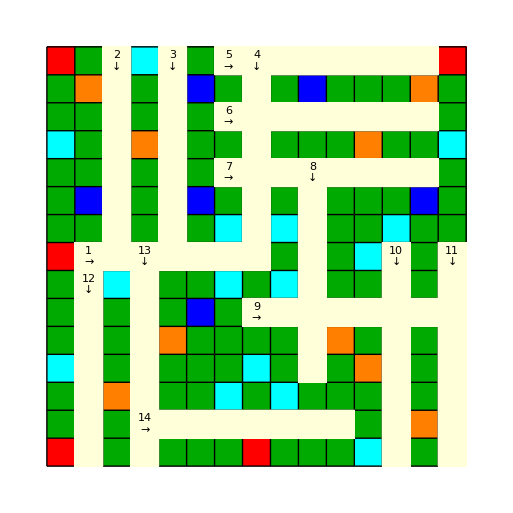

```mathematica
Show[board,Epilog->epilog]
```

```mathematica
(*Animate[turns[i],{i,1,14,1}]*)
```

## Store